# 12 - Catalytic Cracking of Gas Oil

## Fernández Tejada, Adrián Sánchez Loureiro, Adrián

## Obteniendo valores exactos

En primer lugar, calcularemos la proporción de gasoil y gas en el tiempo para estos datos iniciales dados en el Benchmark. Así, una vez calculados, obtendremos las mediciones de concentración z_j en cada instante necesarias para nuestro problema.

```mathematica
θ0 = {12,8,2}
```

{12,8,2}

```mathematica
θ1=θ0 [[1]];
θ2=θ0 [[2]];
θ3=θ0 [[3]];
```

Como se hacen 21 mediciones, hemos divido el intervalo [0,1] en 21 instantes.

```mathematica
ninsts = 21;
insts=Table[i*1./(ninsts-1),{i,0,ninsts-1}];
Length[insts]
```

21

Denotaremos y_1 a la proporción de gasoil e y_2 a la de gasolina. 
Hemos tomado y_1[0] = 1 e y_2[0 ]=0, es decir, comenzámos solo con gasoil.

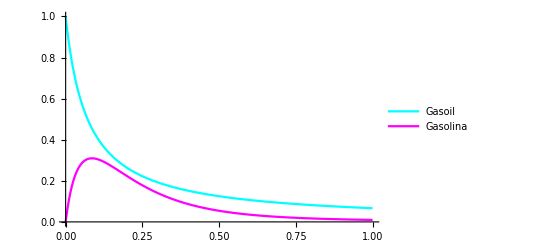

```mathematica
ecssol=NDSolve[{

y1'[t]== -(θ1+θ3)y1[t]*y1[t]   , 
y2'[t]==θ1*y1[t]*y1[t]  - θ2*y2[t],

y1[0]==1, y2[0]==0},{y1[t],y2[t]},

{t,0,1}];

plots={y1[t],y2[t]}/.ecssol;
Show[
Plot[plots[[1,1]],{t,0,1},PlotStyle->Cyan,PlotRange->{{0,1},{0,1}},PlotLegends->{"Gasoil",Cyan}],
Plot[plots[[1,2]],{t,0,1},PlotStyle->Magenta,PlotRange->{{0,1},{0,1}},PlotLegends->{"Gasolina",Magenta}]
]
```

Creamos a partir de la solución obtenida en NDSolve la función soluciones[t]. Esta nos dará los valores exactos de y_1 e y_2 en cada instante t para los valores iniciales θ dados.

```mathematica
soluciones[t_]={y1[t],y2[t]}/.ecssol;
```

Obtenemos para los instantes definidos en insts los valores de y_1 e y_2.

```mathematica
SOL=Flatten[Table[soluciones[k],{k,insts}],1]; (*Valores {Subscript[y, 1], Subscript[y, 2]}*)
SOL1=Table[SOL[[k,1]],{k,1,ninsts}] (*Valores Subscript[y, 1]*)
SOL2=Table[SOL[[k,2]],{k,1,ninsts}] (*Valores Subscript[y, 2]*)
```

{1.,0.588235,0.416667,0.322581,0.263158,0.222222,0.192308,0.169492,0.151515,0.136986,0.125,0.114943,0.106383,0.0990099,0.0925926,0.0869565,0.0819672,0.0775194,0.0735294,0.0699301,0.0666667}

{0.,0.280833,0.306705,0.270935,0.223028,0.178095,0.140312,0.110038,0.0863655,0.0680879,0.054057,0.0433011,0.0350415,0.028673,0.0237334,0.019874,0.0168329,0.014414,0.0124708,0.0108937,0.00960043}

## Obteniendo valores de z

Aplicamos una perturbación relativa aleatoria de 0.1 a los valores exactos de cada instante. Así, definimos los valores de las medidas de concentración z_1 y el z_2 para el problema. Introducimos manualmente las medidas de concentración en el primer instante (comenzamos solo con gasoil).

```mathematica
z1=Table[SOL1[[k]]+SOL1[[k]]*RandomReal[{-0.1,0.1}],{k,1,ninsts}] ;
z2=Table[SOL2[[k]]+SOL2[[k]]*RandomReal[{-0.1,0.1}],{k,1,ninsts}];
z1[[1]]=1.;
z2[[1]] = 0.;
z1
z2
```

{1.,0.607702,0.400274,0.304623,0.285249,0.207525,0.195073,0.179654,0.143929,0.124251,0.114151,0.110992,0.102462,0.108057,0.0936709,0.0903906,0.0895431,0.0774367,0.0757156,0.0712751,0.069858}

{0.,0.25708,0.321813,0.254874,0.223019,0.161687,0.143536,0.119685,0.0856509,0.0645601,0.0506224,0.0464289,0.03312,0.0298002,0.0239137,0.0216534,0.0180759,0.0152526,0.0137041,0.0119513,0.0099552}

Valores de z empleados en el informe.

```mathematica
z1= {1.,0.6347699836831255,0.388832038042773,0.2993403752143724,0.2798377320318468,0.21449317633161508,0.18048680513448762,0.15485515623326518,0.1513021201326371,0.14257911326636935,0.1315771612269763,0.10441612864972143,0.1141623204932389,0.10187743023408839,0.09152416536973931,0.08596399907908388,0.0835082736466175,0.07402553195786021,0.06933645090147744,0.07044205263873547,0.06941467999811421};
z2= {0.,0.2908919075792551,0.307701420909982,0.2936304928086301,0.21685931579500892,0.1717110224067054,0.14338007708238026,0.10869333150487794,0.09171358018260617,0.0746851208990134,0.05624565574102057,0.04441887673120921,0.03578684159544259,0.029132849838211308,0.024418110715885684,0.01934701038815286,0.015732840098499314,0.015794546528213684,0.013227477458176946,0.011862366396319152,0.010050304584443415};
```

## Resolviendo el problema

### Resolution

Limpiamos la variable θ, nuestras variables de decisión.

```mathematica
Clear[θ1,θ2,θ3]
```

Ponemos los valores iniciales.

```mathematica
y1[0]=1;
y2[0]=0;
```

Definimos nuestra lista de variables: y_1, y_2,θ_1,θ_2,θ_3.

```mathematica
Var=Flatten[Join[Flatten[Table[{y1[i],y2[i]},{i,1,ninsts-1}],1],{θ1,θ2,θ3}]]
```

{y1[1],y2[1],y1[2],y2[2],y1[3],y2[3],y1[4],y2[4],y1[5],y2[5],y1[6],y2[6],y1[7],y2[7],y1[8],y2[8],y1[9],y2[9],y1[10],y2[10],y1[11],y2[11],y1[12],y2[12],y1[13],y2[13],y1[14],y2[14],y1[15],y2[15],y1[16],y2[16],y1[17],y2[17],y1[18],y2[18],y1[19],y2[19],y1[20],y2[20],θ1,θ2,θ3}

Definimos las funciones diferenciales restricciones del problema.

```mathematica
f[y1_,y2_]:=  -(θ1+θ3)y1*y1;
g[y1_,y2_]:=θ1*y1*y1  - θ2*y2;
```

Restricciones obtenidas a partir del método de Euler mejorado explícito.

```mathematica
Restricciones=Flatten[Join[
Table[y1[i+1]==y1[i]+(insts[[i+2]]-insts[[i+1]])*(f[y1[i],y2[i]]+f[y1[i+1],y2[i+1]])/2,{i,0,ninsts-2}],
Table[y2[i+1]==y2[i]+(insts[[i+2]]-insts[[i+1]])*(g[y1[i],y2[i]]+g[y1[i+1],y2[i+1]])/2,{i,0,ninsts-2}],
{θ1≥0,θ2≥0,θ3≥0}
]];
```

### Solución

Busquemos un mínimo local y su tiempo de búsqueda.

```mathematica
tmedio = RepeatedTiming[FindMinimum[{Sum[(y1[j]-z1[[j+1]])^2+(y2[j]-z2[[j+1]])^2 ,{j,0,ninsts -1}],Restricciones},Var]][[1]]
FINAL=Timing[FindMinimum[{Sum[(y1[j]-z1[[j+1]])^2+(y2[j]-z2[[j+1]])^2 ,{j,0,ninsts -1}],Restricciones},Var]];
Print["Tiempo de búsqueda -> ",tmedio]
Print["Tiempo de búsqueda -> ",FINAL[[1]]]
Print["Función Objetivo -> ",FINAL[[2,1]]]
Print["Valores de las variables -> ",FINAL[[2,2]]]
FINAL=FINAL[[2]];
```

0.2187

Tiempo de búsqueda -> 0.2187

Tiempo de búsqueda -> 0.313276

Función Objetivo -> 0.00727786

Valores de las variables -> {y1[1]→0.569845,y2[1]→0.295792,y1[2]→0.409857,y2[2]→0.311409,y1[3]→0.321705,y2[3]→0.272645,y1[4]→0.265253,y2[4]→0.224454,y1[5]→0.225844,y2[5]→0.179922,y1[6]→0.196717,y2[6]→0.142532,y1[7]→0.174287,y2[7]→0.112469,y1[8]→0.156474,y2[8]→0.0888257,y1[9]→0.141978,y2[9]→0.0704463,y1[10]→0.129949,y2[10]→0.056236,y1[11]→0.119805,y2[11]→0.0452647,y1[12]→0.111134,y2[12]→0.0367818,y1[13]→0.103636,y2[13]→0.0301995,y1[14]→0.0970877,y2[14]→0.0250647,y1[15]→0.0913191,y2[15]→0.0210324,y1[16]→0.0861986,y2[16]→0.0178413,y1[17]→0.0816226,y2[17]→0.0152942,y1[18]→0.0775085,y2[18]→0.0132423,y1[19]→0.0737898,y2[19]→0.0115734,y1[20]→0.0704119,y2[20]→0.0102027,θ1→10.6272,θ2→7.5945,θ3→2.36133}

Valores de θ obtenido y su comparación con los iniciales

```mathematica
FINAL[[2,{-3,-2,-1}]]
θ0
```

{θ1→10.6272,θ2→7.5945,θ3→2.36133}

{12,8,2}

### Graficando

#### Graficando y_1

Datos obtenidos para y_1 y las mediciones z_1.

```mathematica
FINAL1=Join[{y1[0]},Table[FINAL[[2,1+2*k,2]],{k,0,ninsts -2}]];
z1;
```

Creamos los puntos (y_1[i],i) y (z_1[i],i).

```mathematica
GY1=Transpose[{insts,FINAL1}]
GZ1=Transpose[{insts,z1}]
```

{{0.,1},{0.05,0.569845},{0.1,0.409857},{0.15,0.321705},{0.2,0.265253},{0.25,0.225844},{0.3,0.196717},{0.35,0.174287},{0.4,0.156474},{0.45,0.141978},{0.5,0.129949},{0.55,0.119805},{0.6,0.111134},{0.65,0.103636},{0.7,0.0970877},{0.75,0.0913191},{0.8,0.0861986},{0.85,0.0816226},{0.9,0.0775085},{0.95,0.0737898},{1.,0.0704119}}

{{0.,1.},{0.05,0.63477},{0.1,0.388832},{0.15,0.29934},{0.2,0.279838},{0.25,0.214493},{0.3,0.180487},{0.35,0.154855},{0.4,0.151302},{0.45,0.142579},{0.5,0.131577},{0.55,0.104416},{0.6,0.114162},{0.65,0.101877},{0.7,0.0915242},{0.75,0.085964},{0.8,0.0835083},{0.85,0.0740255},{0.9,0.0693365},{0.95,0.0704421},{1.,0.0694147}}

Graficando y_1 para los valores de tiempo.

```mathematica
Y1=ListLinePlot[GY1,PlotStyle->Purple,PlotRange->All,PlotLegends->{"Gasoil",Purple}];
```

Graficando puntos  (z_1[i],i) para los valores de tiempo.

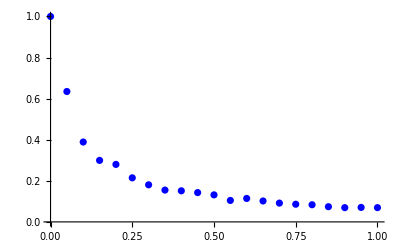

```mathematica
Z1=ListPlot[GZ1,PlotStyle->{Dashed,Blue},PlotRange->All]
```

Graficando ambas anteriores.

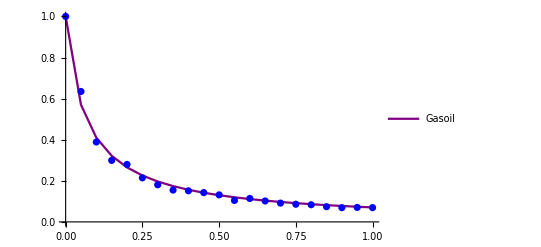

```mathematica
Show[Y1,Z1]
```

#### Graficando y_2

Datos obtenidos para y_2 y las mediciones z_2.

```mathematica
FINAL2=Join[{y2[0]},Table[FINAL[[2,2+2*k,2]],{k,0,ninsts-2}]];
z2;
```

Creamos los puntos (y_2[i],i) y (z_2[i],i).

```mathematica
GY2=Transpose[{insts,FINAL2}];
GZ2=Transpose[{insts,z2}];
```

Graficando y_2 para los valores de tiempo.

```mathematica
Y2=ListLinePlot[GY2,PlotStyle->Red,PlotRange->All,PlotLegends->{"Gasolina",Red}];
```

Graficando puntos  (z_2[i],i) para los valores de tiempo.

```mathematica
Z2=ListPlot[GZ2,PlotStyle->{Dashed,Orange},PlotRange->All];
```

Graficando ambas anteriores.

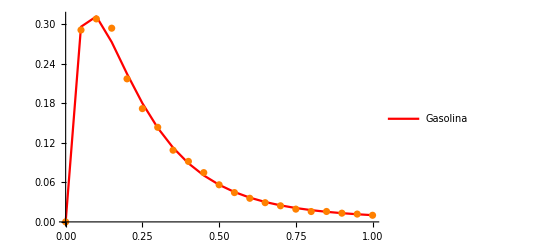

```mathematica
Show[Y2,Z2]
```

#### Graficando y

Unimos todas las gráficas.

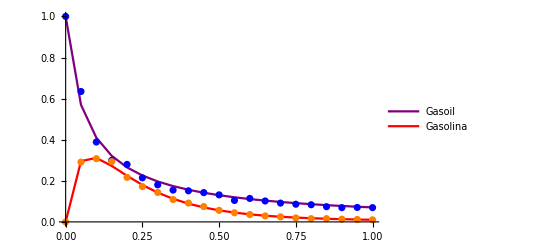

```mathematica
Show[Y1,Y2,Z1,Z2]
```

## Añadiendo pasos

### Resolución

Limpiamos la variable θ, nuestras variables de decisión.

```mathematica
Clear[θ1,θ2,θ3]
```

Ponemos los valores iniciales.

```mathematica
y1[0]=1;
y2[0]=0;
```

Dividimos cada intervalo en subintervalos para poder refinar la gráfica, para ello añadimos npasos puntos intermedios entre los instantes de medición . Las mediciones z se seguiran midiendo en los instantes definidos inicialmente en insts, pero nuestras restricciones se cumpliran para más puntos .

```mathematica
npasos=2;

insts2mit=Table[Table[j*(insts[[i+1]]-insts[[i]])*1./npasos +insts[[i]],{i,1,Length[insts]-1}],{j,1,npasos-1}]
insts2=Sort[Join[Flatten[insts2mit],insts]]
```

{{0.025,0.075,0.125,0.175,0.225,0.275,0.325,0.375,0.425,0.475,0.525,0.575,0.625,0.675,0.725,0.775,0.825,0.875,0.925,0.975}}

{0.,0.025,0.05,0.075,0.1,0.125,0.15,0.175,0.2,0.225,0.25,0.275,0.3,0.325,0.35,0.375,0.4,0.425,0.45,0.475,0.5,0.525,0.55,0.575,0.6,0.625,0.65,0.675,0.7,0.725,0.75,0.775,0.8,0.825,0.85,0.875,0.9,0.925,0.95,0.975,1.}

Vemos gráficicamente los pasos creados.

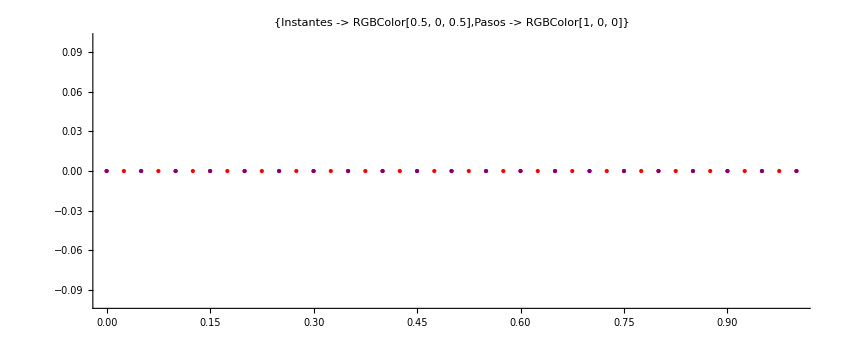

```mathematica
pt1=Table[{insts[[i]],0},{i,1,Length[insts]}];
pt2=Table[{insts2[[i]],0},{i,1,Length[insts2]}];
A1=Graphics[{PointSize[Large],Purple,Point[pt1]},Axes->{True,False}, PlotRange->{{0,1},{-0.1,0.1}}];
A2=Graphics[{PointSize[Medium],Red,Point[pt2]},Axes->{True,False}, PlotRange->{{0,1},{-0.1,0.1}}];
Show[A2,A1,PlotLabel->{"Instantes ->"Purple,"Pasos ->"Red }]
```

Definimos nuestra lista de variables: y_1, y_2,θ_1,θ_2,θ_3.

```mathematica
VarP=Flatten[Join[Flatten[Table[{y1[i],y2[i]},{i,1,Length[insts2]-1}],1],{θ1,θ2,θ3}]];
```

Definimos las funciones diferenciales restricciones del problema.

```mathematica
f[y1_,y2_]:=  -(θ1+θ3)y1*y1;
g[y1_,y2_]:=θ1*y1*y1  - θ2*y2;
```

Restricciones obtenidas a partir del método de Euler mejorado explícito.

```mathematica
RestriccionesP=Flatten[Join[
Table[y1[i+1]==y1[i]+(insts2[[i+2]]-insts2[[i+1]])*(f[y1[i],y2[i]]+f[y1[i+1],y2[i+1]])/2,{i,0,Length[insts2]-2}],
Table[y2[i+1]==y2[i]+(insts2[[i+2]]-insts2[[i+1]])*(g[y1[i],y2[i]]+g[y1[i+1],y2[i+1]])/2,{i,0,Length[insts2]-2}],
{θ1≥0,θ2≥0,θ3≥0}
]];
```

Definimos nuestra función objetivo para los z medidos en los 21 instantes.

```mathematica
FObjP= Sum[(y1[npasos*j]-z1[[j+1]])^2+(y2[npasos*j]-z2[[j+1]])^2 ,{j,0,Length[insts]-1}];
```

### Solución

Busquemos un mínimo local y su tiempo de búsqueda.

```mathematica
tmediop = RepeatedTiming[FindMinimum[{FObjP,RestriccionesP},VarP]][[1]]
Print["Tiempo de búsqueda -> ",tmediop]
FINALP=Timing[FindMinimum[{FObjP,RestriccionesP},VarP]];
Print["Tiempo de búsqueda -> ",FINALP[[1]]]
Print["Función Objetivo -> ",FINALP[[2,1]]]
Print["Valores de las variables -> ",FINALP[[2,2]]]
FINALP=FINALP[[2]];
```

0.174048

Tiempo de búsqueda -> 0.174048

Tiempo de búsqueda -> 0.515297

Función Objetivo -> 0.00543111

Valores de las variables -> {y1[1]→0.734548,y2[1]→0.20915,y1[2]→0.582927,y2[2]→0.290708,y1[3]→0.483955,y2[3]→0.316004,y1[4]→0.414017,y2[4]→0.313839,y1[5]→0.361882,y2[5]→0.29804,y1[6]→0.321482,y2[6]→0.275858,y1[7]→0.289238,y2[7]→0.25127,y1[8]→0.262897,y2[8]→0.226487,y1[9]→0.240968,y2[9]→0.202719,y1[10]→0.222426,y2[10]→0.18059,y1[11]→0.206541,y2[11]→0.160378,y1[12]→0.192778,y2[12]→0.142157,y1[13]→0.180738,y2[13]→0.12588,y1[14]→0.170115,y2[14]→0.111436,y1[15]→0.160674,y2[15]→0.0986796,y1[16]→0.152228,y2[16]→0.0874514,y1[17]→0.144626,y2[17]→0.0775923,y1[18]→0.137748,y2[18]→0.0689496,y1[19]→0.131495,y2[19]→0.0613807,y1[20]→0.125785,y2[20]→0.0547552,y1[21]→0.120552,y2[21]→0.0489557,y1[22]→0.115736,y2[22]→0.0438775,y1[23]→0.111291,y2[23]→0.039428,y1[24]→0.107175,y2[24]→0.0355256,y1[25]→0.103353,y2[25]→0.0320989,y1[26]→0.099794,y2[26]→0.0290858,y1[27]→0.0964721,y2[27]→0.0264319,y1[28]→0.0933645,y2[28]→0.0240902,y1[29]→0.0904508,y2[29]→0.02202,y1[30]→0.0877137,y2[30]→0.020186,y1[31]→0.0851373,y2[31]→0.0185576,y1[32]→0.0827081,y2[32]→0.0171085,y1[33]→0.0804137,y2[33]→0.0158157,y1[34]→0.0782432,y2[34]→0.0146596,y1[35]→0.0761868,y2[35]→0.0136231,y1[36]→0.0742358,y2[36]→0.0126914,y1[37]→0.0723823,y2[37]→0.0118518,y1[38]→0.0706191,y2[38]→0.0110931,y1[39]→0.0689397,y2[39]→0.0104059,y1[40]→0.0673384,y2[40]→0.00978172,θ1→11.951,θ2→7.97145,θ3→1.8427}

Valores de θ obtenido, comparados con los iniciales y los obtenidos anteriormente.

```mathematica
Print["Valores obtenidos en este apartado: "]
FINALP[[2,{-3,-2,-1}]]
Print["Valores sin puntos intermedios: "]
FINAL[[2,{-3,-2,-1}]]
Print["Valores iniciales: "]
θ0
```

Valores obtenidos en este apartado:

{θ1→11.951,θ2→7.97145,θ3→1.8427}

Valores sin puntos intermedios:

{θ1→10.6272,θ2→7.5945,θ3→2.36133}

Valores iniciales:

{12,8,2}

### Graficando

#### Graficando y_1

Datos obtenidos para y_1 y las mediciones z_1.

```mathematica
FINALP1=Join[{y1[0]},Table[FINALP[[2,1+2*k,2]],{k,0,Length[insts2]-2}]];
z1;
```

Creamos los puntos (y_1[i],i) y (z_1[i],i).

```mathematica
GYP1=Transpose[{insts2,FINALP1}];
```

Graficando y_1 para los valores de tiempo.

```mathematica
YP1=ListLinePlot[GYP1,PlotStyle->Green,PlotRange->All,PlotLegends->{"Gasoil con pasos",Green}];
```

Graficando ambas anteriores.

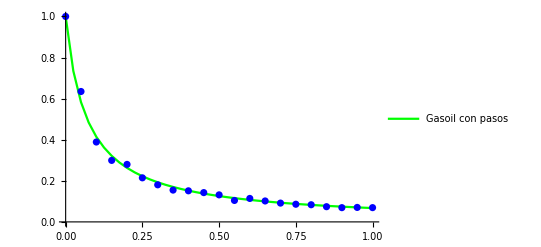

```mathematica
Show[YP1,Z1]
```

Comparamos las gráficas obtenida sin puntos intermedios y la obtenida ahora.

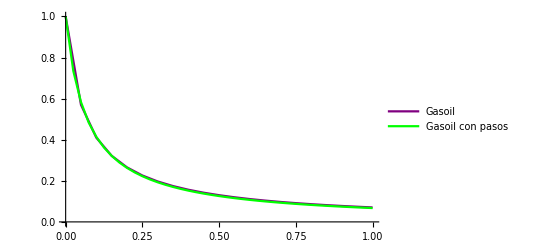

```mathematica
Show[Y1,YP1]
```

#### Graficando y_2

Datos obtenidos para y_2 y las mediciones z_2.

```mathematica
FINALP2=Join[{y2[0]},Table[FINALP[[2,2+2*k,2]],{k,0,Length[insts2]-2}]];
z2;
```

Creamos los puntos (y_2[i],i) y (z_2[i],i).

```mathematica
GYP2=Transpose[{insts2,FINALP2}];
```

Graficando y_2 para los valores de tiempo.

```mathematica
YP2=ListLinePlot[GYP2,PlotStyle->Magenta,PlotRange->All,PlotLegends->{"Gasolina con pasos",Magenta}];
```

Graficando ambas anteriores.

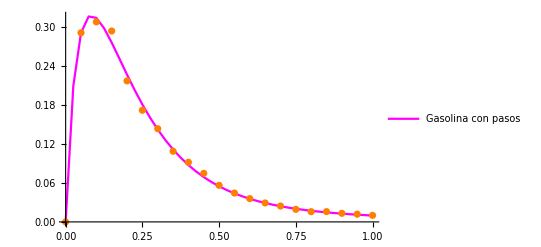

```mathematica
Show[YP2,Z2]
```

Comparamos las gráficas obtenida sin puntos intermedios y la obtenida ahora.

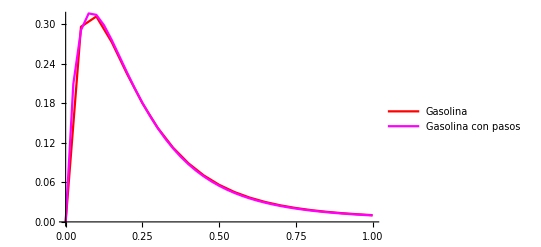

```mathematica
Show[Y2,YP2]
```

#### Graficando y

Unimos todas las gráficas refinadas obtenidas a partir de la partición de los intervalos.

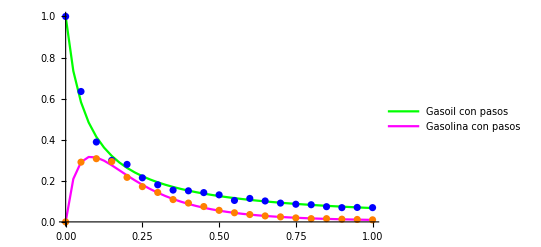

```mathematica
Show[YP1,YP2,Z1,Z2]
```

Y podemos observar la diferencia con las gráficas iniciales de solo 21 instantes.

```mathematica
Show[Y1,Y2,Z1,Z2]
```

-Graphics-

Ambas gráficas unidas.

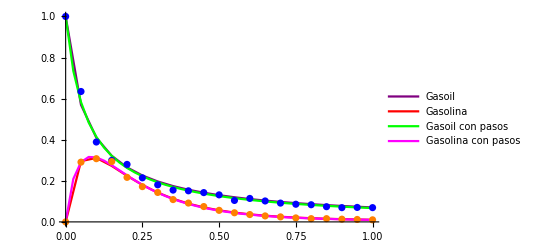

```mathematica
Show[Y1,Y2,YP1,YP2,Z1,Z2]
```

## Introduciendo datos en AMPL

### Datos

En primer lugar indicamos el número de instantes de nuestro problema y el número de pasos que daremos cuando hagamos la implementación. Dividimos el intervalo [0,1] en 21 instantes, y metermos los pasos intermedios necesarios. Y definimos los valores de z que hemos usado en apartados anteriores.

```mathematica
ninstsP = 21;
npasosP=4;

instsP=Table[i*1./(ninstsP-1),{i,0,ninstsP-1}];
insts2mitP=Table[Table[j*(instsP[[i+1]]-instsP[[i]])*1./npasosP +instsP[[i]],{i,1,Length[instsP]-1}],{j,1,npasosP-1}];
insts2P=Sort[Join[Flatten[insts2mitP],instsP]];

z1P= {1,0.6347699836831255,0.388832038042773,0.2993403752143724,0.2798377320318468,0.21449317633161508,0.18048680513448762,0.15485515623326518,0.1513021201326371,0.14257911326636935,0.1315771612269763,0.10441612864972143,0.1141623204932389,0.10187743023408839,0.09152416536973931,0.08596399907908388,0.0835082736466175,0.07402553195786021,0.06933645090147744,0.07044205263873547,0.06941467999811421};
z2P= {0,0.2908919075792551,0.307701420909982,0.2936304928086301,0.21685931579500892,0.1717110224067054,0.14338007708238026,0.10869333150487794,0.09171358018260617,0.0746851208990134,0.05624565574102057,0.04441887673120921,0.03578684159544259,0.029132849838211308,0.024418110715885684,0.01934701038815286,0.015732840098499314,0.015794546528213684,0.013227477458176946,0.011862366396319152,0.010050304584443415};
```

### Problema estándar

#### Ruta

Esta es la ruta para acceder al archivo que leerá AMPL.

```mathematica
ruta=FileNameJoin[{$HomeDirectory,"Documents/UNI/PNLCC/PRACTICAS/12-CRACKING/AMPL/ESTANDAR","cracking.dat"}];
```

#### Insertando datos

En este apartado vemos como hemos escrito el documento de los datos de las mediciones z para que las pueda usar AMPL. Usando por texto funciones que usa AMPL y nuestros datos.

```mathematica
(*Elimina el archivo*)
DeleteFile[ruta]
```

```mathematica
(*Abrir el archivo en modo de escritura*)
salida=OpenWrite[ruta];

(*Escribir el contenido*)
WriteString[salida,StringJoin["let NODES ",":= ",TextString[ninstsP],";\n"]];
Do[WriteString[salida,StringJoin["let z1[",TextString[i-1],"] := ",TextString[z1P[[i]]],";\n"]],{i,1,Length[z1P]}];
Do[WriteString[salida,StringJoin["let z2[",TextString[i-1],"] := ",TextString[z2P[[i]]],";\n"]],{i,1,Length[z2P]}];

(*Cerrar el archivo en modo de escritura*)
Close[salida];
```

#### Salida

Aquí podemos observar el contenido del archivo que hemos creado.

```mathematica
(*Abrir el archivo en modo de lectura*)
entrada=OpenRead[ruta];
(*Leer el contenido anterior del archivo línea por línea*)
contenido=ReadList[entrada,String]

(*Cerrar el archivo en modo de lectura*)
Close[entrada];
```

{let NODES := 21;,let z1[0] := 1;,let z1[1] := 0.63477;,let z1[2] := 0.388832;,let z1[3] := 0.29934;,let z1[4] := 0.279838;,let z1[5] := 0.214493;,let z1[6] := 0.180487;,let z1[7] := 0.154855;,let z1[8] := 0.151302;,let z1[9] := 0.142579;,let z1[10] := 0.131577;,let z1[11] := 0.104416;,let z1[12] := 0.114162;,let z1[13] := 0.101877;,let z1[14] := 0.0915242;,let z1[15] := 0.085964;,let z1[16] := 0.0835083;,let z1[17] := 0.0740255;,let z1[18] := 0.0693365;,let z1[19] := 0.0704421;,let z1[20] := 0.0694147;,let z2[0] := 0;,let z2[1] := 0.290892;,let z2[2] := 0.307701;,let z2[3] := 0.29363;,let z2[4] := 0.216859;,let z2[5] := 0.171711;,let z2[6] := 0.14338;,let z2[7] := 0.108693;,let z2[8] := 0.0917136;,let z2[9] := 0.0746851;,let z2[10] := 0.0562457;,let z2[11] := 0.0444189;,let z2[12] := 0.0357868;,let z2[13] := 0.0291328;,let z2[14] := 0.0244181;,let z2[15] := 0.019347;,let z2[16] := 0.0157328;,let z2[17] := 0.0157945;,let z2[18] := 0.0132275;,let z2[19] := 0.0118624;,let z2[20] := 0.0100503;}

### Problema añadiendo puntos intermedios

#### Ruta

Ahora hacemos el mismo procedimiento anterior para la nueva ruta que almacenará el archivo de pasos intermedios, en el cual escribiremos nuestros datos z y los instantes con puntos intermedios.

```mathematica
rutaP=FileNameJoin[{$HomeDirectory,"Documents/UNI/PNLCC/PRACTICAS/12-CRACKING/AMPL/PASOS","cracking_pasos.dat"}];
```

#### Insertando datos

```mathematica
(*Elimina el archivo*)
DeleteFile[rutaP]
```

```mathematica
(*Abrir el archivo en modo de escritura*)
salidaP=OpenWrite[rutaP];

(*Escribir el contenido*)
WriteString[salidaP,StringJoin["let NODES ",":= ",TextString[ninstsP],";\n"]];
WriteString[salidaP,StringJoin["let npasos ",":= ",TextString[npasosP],";\n"]]
Do[WriteString[salidaP,StringJoin["let z1[",TextString[i-1],"] := ",TextString[z1P[[i]]],";\n"]],{i,1,Length[z1P]}];
Do[WriteString[salidaP,StringJoin["let z2[",TextString[i-1],"] := ",TextString[z2P[[i]]],";\n"]],{i,1,Length[z2P]}];
Do[WriteString[salidaP,StringJoin["let insts2[",TextString[i-1],"] := ",TextString[insts2P[[i]]],";\n"]],{i,1,Length[insts2P]}];

(*Cerrar el archivo en modo de escritura*)
Close[salidaP];
```

#### Salida

```mathematica
(*Abrir el archivo en modo de lectura*)
entradaP=OpenRead[rutaP];
(*Leer el contenido anterior del archivo línea por línea*)
contenidoP=ReadList[entradaP,String]

(*Cerrar el archivo en modo de lectura*)
Close[entradaP];
```

{let NODES := 21;,let npasos := 4;,let z1[0] := 1;,let z1[1] := 0.63477;,let z1[2] := 0.388832;,let z1[3] := 0.29934;,let z1[4] := 0.279838;,let z1[5] := 0.214493;,let z1[6] := 0.180487;,let z1[7] := 0.154855;,let z1[8] := 0.151302;,let z1[9] := 0.142579;,let z1[10] := 0.131577;,let z1[11] := 0.104416;,let z1[12] := 0.114162;,let z1[13] := 0.101877;,let z1[14] := 0.0915242;,let z1[15] := 0.085964;,let z1[16] := 0.0835083;,let z1[17] := 0.0740255;,let z1[18] := 0.0693365;,let z1[19] := 0.0704421;,let z1[20] := 0.0694147;,let z2[0] := 0;,let z2[1] := 0.290892;,let z2[2] := 0.307701;,let z2[3] := 0.29363;,let z2[4] := 0.216859;,let z2[5] := 0.171711;,let z2[6] := 0.14338;,let z2[7] := 0.108693;,let z2[8] := 0.0917136;,let z2[9] := 0.0746851;,let z2[10] := 0.0562457;,let z2[11] := 0.0444189;,let z2[12] := 0.0357868;,let z2[13] := 0.0291328;,let z2[14] := 0.0244181;,let z2[15] := 0.019347;,let z2[16] := 0.0157328;,let z2[17] := 0.0157945;,let z2[18] := 0.0132275;,let z2[19] := 0.0118624;,let z2[20] := 0.0100503;,let insts2[0] := 0.0;,let insts2[1] := 0.0125;,let insts2[2] := 0.025;,let insts2[3] := 0.0375;,let insts2[4] := 0.05;,let insts2[5] := 0.0625;,let insts2[6] := 0.075;,let insts2[7] := 0.0875;,let insts2[8] := 0.1;,let insts2[9] := 0.1125;,let insts2[10] := 0.125;,let insts2[11] := 0.1375;,let insts2[12] := 0.15;,let insts2[13] := 0.1625;,let insts2[14] := 0.175;,let insts2[15] := 0.1875;,let insts2[16] := 0.2;,let insts2[17] := 0.2125;,let insts2[18] := 0.225;,let insts2[19] := 0.2375;,let insts2[20] := 0.25;,let insts2[21] := 0.2625;,let insts2[22] := 0.275;,let insts2[23] := 0.2875;,let insts2[24] := 0.3;,let insts2[25] := 0.3125;,let insts2[26] := 0.325;,let insts2[27] := 0.3375;,let insts2[28] := 0.35;,let insts2[29] := 0.3625;,let insts2[30] := 0.375;,let insts2[31] := 0.3875;,let insts2[32] := 0.4;,let insts2[33] := 0.4125;,let insts2[34] := 0.425;,let insts2[35] := 0.4375;,let insts2[36] := 0.45;,let insts2[37] := 0.4625;,let insts2[38] := 0.475;,let insts2[39] := 0.4875;,let insts2[40] := 0.5;,let insts2[41] := 0.5125;,let insts2[42] := 0.525;,let insts2[43] := 0.5375;,let insts2[44] := 0.55;,let insts2[45] := 0.5625;,let insts2[46] := 0.575;,let insts2[47] := 0.5875;,let insts2[48] := 0.6;,let insts2[49] := 0.6125;,let insts2[50] := 0.625;,let insts2[51] := 0.6375;,let insts2[52] := 0.65;,let insts2[53] := 0.6625;,let insts2[54] := 0.675;,let insts2[55] := 0.6875;,let insts2[56] := 0.7;,let insts2[57] := 0.7125;,let insts2[58] := 0.725;,let insts2[59] := 0.7375;,let insts2[60] := 0.75;,let insts2[61] := 0.7625;,let insts2[62] := 0.775;,let insts2[63] := 0.7875;,let insts2[64] := 0.8;,let insts2[65] := 0.8125;,let insts2[66] := 0.825;,let insts2[67] := 0.8375;,let insts2[68] := 0.85;,let insts2[69] := 0.8625;,let insts2[70] := 0.875;,let insts2[71] := 0.8875;,let insts2[72] := 0.9;,let insts2[73] := 0.9125;,let insts2[74] := 0.925;,let insts2[75] := 0.9375;,let insts2[76] := 0.95;,let insts2[77] := 0.9625;,let insts2[78] := 0.975;,let insts2[79] := 0.9875;,let insts2[80] := 1.0;}

### Graficando datos obtenidos por AMPL

#### Problema estándar

Tomamos la ruta donde se guarda la solución de nuestro problema estándar, y leemos el archivo que hemos creado adaptado para poder graficar los valores obtenidos.

```mathematica
ruta1=FileNameJoin[{$HomeDirectory,"Documents/UNI/PNLCC/PRACTICAS/12-CRACKING/AMPL/ESTANDAR","output_mat.txt"}];

(*Abrir el archivo en modo de lectura*)
entrada1=OpenRead[ruta1];

(*Leer el contenido anterior del archivo línea por línea*)
contenido1=ReadList[entrada1,String];

(*Cerrar el archivo en modo de lectura*)
Close[entrada1];
```

Separamos la lista de caracteres que hemos leido justo donde se encuentra la fila de guiones.

```mathematica
lista1 = Split[contenido1,#1!="---------------------------------------"&&#2!="&"&];
```

Y por último, con este búcle pintaremos nuestras gráficas, quitandoles el último carácter a cada lista con la función Most, y separando con Split donde se encuentre un espacio. Asi ya hemos creado un vector en el que se encuentra el nombre del solver, θ, y_1 e y_2. Y hacemos las gráficas del gasoil y la gasolina, uniendoles los puntos de las mediciones z.

SOLVER -> MINOS 5.51

Thetas -> {10.6272,7.59451,2.36133}

-Graphics-

SOLVER -> LOQO 7.03

Thetas -> {10.6272,7.5945,2.36133}

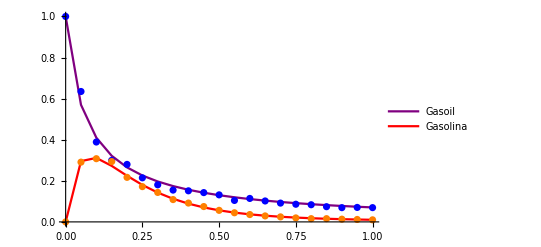

SOLVER -> CONOPT 3.17A

Thetas -> {10.6272,7.5945,2.36133}

-Graphics-

SOLVER -> SNOPT 7.5-1.2

Thetas -> {10.6272,7.5945,2.36133}

-Graphics-

```mathematica
For[i=1,i<= Length[lista1],i++,
	datos1 = Split[Most[lista1[[i]]],#1!=" "&&#2!="&"&];
	nombre = Most[datos1[[1]]] ;
	thetas =  ToExpression[Most[datos1[[2]]]];
	y1s =ToExpression[ Most[datos1[[3]]] ];
	y2s =ToExpression[ datos1[[4]]];
	
	GY1=Transpose[{insts,y1s}];
	Y1=ListLinePlot[GY1,PlotStyle->Purple,PlotRange->All,PlotLegends->{"Gasoil",Purple}];
	GY2=Transpose[{insts,y2s}];
	Y2=ListLinePlot[GY2,PlotStyle->Red,PlotRange->All,PlotLegends->{"Gasolina",Red}];
	
	Print["SOLVER -> ",nombre[[1]] ];
	Print["Thetas -> ",Text[thetas] ];
	Print[Show[Y1,Y2,Z1,Z2]]
]
```

#### Problema con pasos

Procedemos como en el apartado anterior, pero ahora graficaremos la implementación de pasos en nuestras soluciones.

```mathematica
ruta2=FileNameJoin[{$HomeDirectory,"Documents/UNI/PNLCC/PRACTICAS/12-CRACKING/AMPL/PASOS","output_pasos_mat.txt"}];

(*Abrir el archivo en modo de lectura*)
entrada2=OpenRead[ruta2];

(*Leer el contenido anterior del archivo línea por línea*)
contenido2=ReadList[entrada2,String];

(*Cerrar el archivo en modo de lectura*)
Close[entrada2];
```

```mathematica
lista2 = Split[contenido2,#1!="---------------------------------------"&&#2!="&"&];
```

```mathematica
For[i=1,i<= Length[lista2],i++,
	datos1 = Split[Most[lista2[[i]]],#1!=" "&&#2!="&"&];
	nombre = Most[datos1[[1]]] ;
	thetas =  ToExpression[Most[datos1[[2]]]];
	y1s =ToExpression[ Most[datos1[[3]]] ];
	y2s =ToExpression[ datos1[[4]]];
	
	GYP1=Transpose[{insts2,FINALP1}];
	YP1=ListLinePlot[GYP1,PlotStyle->Green,PlotRange->All,PlotLegends->{"Gasoil con pasos",Green}];

	GYP2=Transpose[{insts2,FINALP2}];
	YP2=ListLinePlot[GYP2,PlotStyle->Magenta,PlotRange->All,PlotLegends->{"Gasolina con pasos",Magenta}];
	
	Print["SOLVER -> ",nombre[[1]] ];
	Print["Thetas -> ",Text[thetas] ];
	Print[Show[YP1,YP2,Z1,Z2]]
]
```

SOLVER -> MINOS 5.51

Thetas -> {12.2971,8.06856,1.69651}

-Graphics-

SOLVER -> LOQO 7.03

Thetas -> {12.2969,8.06849,1.6965}

-Graphics-

SOLVER -> CONOPT 3.17A

Thetas -> {12.2971,8.06856,1.69651}

-Graphics-

SOLVER -> SNOPT 7.5-1.2

Thetas -> {12.2971,8.06856,1.69651}

-Graphics-